# Unit 2: Differentiation

## Linear approximation

```mathematica
10*0.4+150
```

154.

-Graphics-

```mathematica
D[√x,x]
```

1/(2 √x)

```mathematica
1/(2 √100)
```

1/20

```mathematica
4*%
```

1/5

```mathematica
f[x_]:=x^2.5
f'[4]*-0.03+f[4]
```

31.4

```mathematica
D[√x,{x,2}]
```

-1/(4 x^(3/2))

```mathematica
-1/(4 100^(3/2))
```

-1/4000

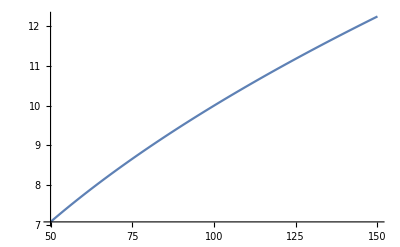

```mathematica
Plot[√x,{x,50,150}]
```

```mathematica
v[x_]:=4π*x^3/3
v'[r]
v'[10]*-0.03
```

4 π r^2

-37.6991

```mathematica
v'[10]
```

400 π

```mathematica
20/400
```

1/20

## Product rule

```mathematica
D[√x,x]*Cos[x]+√x*-Sin[x]
```

Cos[x]/(2 √x)-√x Sin[x]

```mathematica
100*0.4
```

40.

```mathematica
100*-0.01+3*0.4
```

0.2

f(x)=x^2 Sin[x]Cos[x]
f'[x]=2x*Sin[x]*Cos[x]
		 + x^2*-Cos[x] *Sin[x]
	 	+ x^2* Sin[x]*-Sin[x]

## Quotient Rule

```mathematica
Limit[(f2*g-f*g2)/t,t->0]
```

Indeterminate

```mathematica
D[(2+Cos[X])/(x^2+1),x]
```

-(2 x (2+Cos[X]))/((1+x^2)^2)

-Graphics-

## Chain rule

```mathematica
D[120*t+100,t]
```

120

```mathematica
3*0.01+9
```

9.03

```mathematica
4*(9.03-9)+5
```

5.12

```mathematica
Solve[5.12==x*(2.01-2)+5,x]
```

{{x→12.}}

```mathematica
3*4*(5*2)
```

120

#### Examples

```mathematica
f[x_]:=√(x^3+2x+1)
f1[x_]:=1/(2 √(x^3+2x+1))*(3 x^2+2)
f1[1]
```

5/4

```mathematica
g[x_]:=Sin[x^2+2x]
g1[x_]:=-Cos[x^2+2x]*(2x+2)
g1[x]
```

(2+2 x) Cos[2 x+x^2]

#### Exercises

```mathematica
f[x_]:=Sin[x/(x^2+1)]
f1[x_]:= Cos[u]*u'
f2[x_]:= Cos[x/(x^2+1)]*((x^2+1)-(x*2*x))/((x^2+1)^2)
f2[x]==f'[x]
f2[x]
```

True

(-(2 x^2)/((1+x^2)^2)+1/(1+x^2)) Cos[x/(1+x^2)]

```mathematica
k[x_]:=Cos[x]*Sin[x]^4
u:= Sin[x]^4
k1[x_]:= -Sin[x]*u+Cos[x]*u'
inn:= Sin[x]
auss:= x^4
k2[x_]:= -Sin[x]*Sin[x]^4+Cos[x]*(4*(Sin[x])^3*Cos[x])
k'[x] == k2[x]
k2[x]
```

True

4 Cos[x]^2 Sin[x]^3-Sin[x]^5

### Review

```mathematica
g'[f[3]]*f'[3];
g'[5]*3;
4*3

f'[g[3]]*g'(3);
f'[4]*5;
-3*5
```

12

-15

```mathematica
p[i_]:=10*i^2
p'[6]
```

120